```mathematica
tf1=0.24*Pi
```

0.753982

```mathematica
η[t_,tf_]:= (t/tf)^3(1+3(1-(t/tf))+6(1-(t/tf))^2)
```

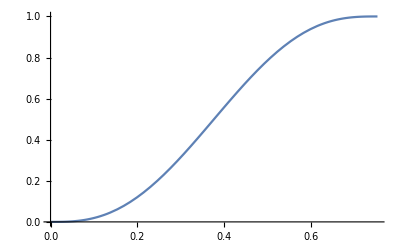

```mathematica
Plot[ η[t,tf1],{t,0,tf1}]
```

```mathematica
D[ η[t,tf],t]
```

(3 t^2 (1+3 (1-t/tf)+6 (1-t/tf)^2))/tf^3+(t^3 (-3/tf-(12 (1-t/tf))/tf))/tf^3

```mathematica
η[t,tf1]
```

2.33301 (1+3 (1-1.32629 t)+6 (1-1.32629 t)^2) t^3

```mathematica
ψ[x_,ξ_]:=ξ^(1/4)/Pi^(1/4)Exp[-ξ/2 *x^2]
```

```mathematica
a=1.0/3.0
```

0.333333

```mathematica
b=1.0/4.0
```

0.25

```mathematica
ρ1[x_,t_,tf_,ξ1_,ξ2_]:=(1- η[t,tf])ψ[x,ξ1]+η[t,tf]*ψ[x,ξ2]
```

```mathematica
Norma[t_,tf_,ξ1_,ξ2_]:=Integrate[ρ1[x,t,tf,ξ1,ξ2]*ρ1[x,t,tf,ξ1,ξ2],{x,-∞,∞}]
```

```mathematica
FullSimplify[Norma[t,tf1,a,b]-(1- η[t,tf1])^2-η[t,tf1]^2-2*(1- η[t,tf1]) η[t,tf1]*Sqrt[2Sqrt[a*b]/(a+b)]]
```

2.22045×10^-16+t^3 (-5.07927×10^-15+t (-8.71525×10^-15+t (-1.10467×10^-14+t (-1.13687×10^-13+t (-4.54747×10^-13-1.81899×10^-12 t+3.41061×10^-13 t^3)))))

```mathematica
Znor[t_,tf_,ξ1_,ξ2_]:=(1- η[t,tf])^2+η[t,tf]^2+2*(1- η[t,tf]) η[t,tf]*Sqrt[2Sqrt[ξ1*ξ2]/(ξ1+ξ2)]
```

```mathematica
ρ[x_,t_,tf_,ξ1_,ξ2_]:=ρ1[x,t,tf,ξ1,ξ2]/Sqrt[Znor[t,tf,ξ1,ξ2]]
```

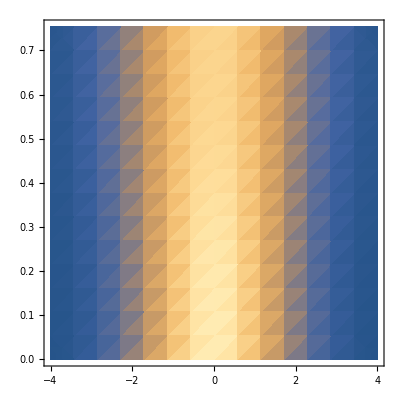

```mathematica
DensityPlot[ρ[x,t,tf1,a,b]^2,{x,-4,4},{t,0,tf1}]
```

```mathematica
Uvel[x_,t_,tf_,ξ1_,ξ2_]:=1/ρ[x,t,tf,ξ1,ξ2]^2 D[Integrate[ρ[u,t,tf,ξ1,ξ2]^2,{u,0,x}],t]
```

```mathematica
DensityPlot[Uvel[x,t,tf1,a,b],{x,-4,4},{t,0,tf1}]
```

-Graphics-

```mathematica
1/ρ[x,t,tf,ξ1,ξ2]^2 D[Integrate[ρ[u,t,tf,ξ1,ξ2]^2,{u,0,x}],t]
```

(((1-(t^3 (1+3 (1-t/tf)+6 (1-t/tf)^2))/tf^3)^2+(t^6 (1+3 (1-t/tf)+6 (1-t/tf)^2)^2)/tf^6+(2 √2 t^3 (1+3 (1-t/tf)+6 (1-t/tf)^2) (1-(t^3 (1+3 (1-t/tf)+6 (1-t/tf)^2))/tf^3) √((√(ξ1 ξ2))/(ξ1+ξ2)))/tf^3) ((x (2 (t-tf)^6 (12 t+3 tf) (6 t^2+3 t tf+tf^2) √ξ1 √(x^2 ξ2) √(x^2 (ξ1+ξ2)) Erf[√(x^2 ξ1)]+6 (t-tf)^5 (6 t^2+3 t tf+tf^2)^2 √ξ1 √(x^2 ξ2) √(x^2 (ξ1+ξ2)) Erf[√(x^2 ξ1)]+t^3 (6 t^2-15 t tf+10 tf^2) √(x^2 ξ1) ξ2^(1/4) (t^3 (12 t-15 tf) ξ2^(1/4) √(x^2 (ξ1+ξ2)) Erf[√(x^2 ξ2)]+3 t^2 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4) √(x^2 (ξ1+ξ2)) Erf[√(x^2 ξ2)]-2 √2 (t-tf)^3 (12 t+3 tf) ξ1^(1/4) √(x^2 ξ2) Erf[(√(x^2 (ξ1+ξ2)))/(√2)]-6 √2 (t-tf)^2 (6 t^2+3 t tf+tf^2) ξ1^(1/4) √(x^2 ξ2) Erf[(√(x^2 (ξ1+ξ2)))/(√2)])+t^3 (12 t-15 tf) √(x^2 ξ1) ξ2^(1/4) (t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4) √(x^2 (ξ1+ξ2)) Erf[√(x^2 ξ2)]-2 √2 (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4) √(x^2 ξ2) Erf[(√(x^2 (ξ1+ξ2)))/(√2)])+3 t^2 (6 t^2-15 t tf+10 tf^2) √(x^2 ξ1) ξ2^(1/4) (t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4) √(x^2 (ξ1+ξ2)) Erf[√(x^2 ξ2)]-2 √2 (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4) √(x^2 ξ2) Erf[(√(x^2 (ξ1+ξ2)))/(√2)])))/(2 √(x^2 ξ1) √(x^2 ξ2) √(x^2 (ξ1+ξ2)) ((t-tf)^6 (6 t^2+3 t tf+tf^2)^2+t^6 (6 t^2-15 t tf+10 tf^2)^2-2 √2 t^3 (t-tf)^3 (6 t^2+3 t tf+tf^2) (6 t^2-15 t tf+10 tf^2) √((√(ξ1 ξ2))/(ξ1+ξ2))))-(x (2 (t-tf)^6 (12 t+3 tf) (6 t^2+3 t tf+tf^2)+6 (t-tf)^5 (6 t^2+3 t tf+tf^2)^2+2 t^6 (12 t-15 tf) (6 t^2-15 t tf+10 tf^2)+6 t^5 (6 t^2-15 t tf+10 tf^2)^2-2 √2 t^3 (12 t-15 tf) (t-tf)^3 (6 t^2+3 t tf+tf^2) √((√(ξ1 ξ2))/(ξ1+ξ2))-2 √2 t^3 (t-tf)^3 (12 t+3 tf) (6 t^2-15 t tf+10 tf^2) √((√(ξ1 ξ2))/(ξ1+ξ2))-6 √2 t^3 (t-tf)^2 (6 t^2+3 t tf+tf^2) (6 t^2-15 t tf+10 tf^2) √((√(ξ1 ξ2))/(ξ1+ξ2))-6 √2 t^2 (t-tf)^3 (6 t^2+3 t tf+tf^2) (6 t^2-15 t tf+10 tf^2) √((√(ξ1 ξ2))/(ξ1+ξ2))) ((t-tf)^6 (6 t^2+3 t tf+tf^2)^2 √ξ1 √(x^2 ξ2) √(x^2 (ξ1+ξ2)) Erf[√(x^2 ξ1)]+t^3 (6 t^2-15 t tf+10 tf^2) √(x^2 ξ1) ξ2^(1/4) (t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4) √(x^2 (ξ1+ξ2)) Erf[√(x^2 ξ2)]-2 √2 (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4) √(x^2 ξ2) Erf[(√(x^2 (ξ1+ξ2)))/(√2)])))/(2 √(x^2 ξ1) √(x^2 ξ2) √(x^2 (ξ1+ξ2)) ((t-tf)^6 (6 t^2+3 t tf+tf^2)^2+t^6 (6 t^2-15 t tf+10 tf^2)^2-2 √2 t^3 (t-tf)^3 (6 t^2+3 t tf+tf^2) (6 t^2-15 t tf+10 tf^2) √((√(ξ1 ξ2))/(ξ1+ξ2)))^2)))/((ⅇ^(-(x^2 ξ1)/2) (1-(t^3 (1+3 (1-t/tf)+6 (1-t/tf)^2))/tf^3) ξ1^(1/4))/π^(1/4)+(ⅇ^(-(x^2 ξ2)/2) t^3 (1+3 (1-t/tf)+6 (1-t/tf)^2) ξ2^(1/4))/(π^(1/4) tf^3))^2

```mathematica
FullSimplify[%59]
```

-((30 ⅇ^(x^2 (ξ1+ξ2)) √π t^2 (t-tf)^2 tf^5 ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[x √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[x √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(x √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((x^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((x^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2))))))

```mathematica
VelHid[x_,t_,tf_,ξ1_,ξ2_]:=-((30 ⅇ^(x^2 (ξ1+ξ2)) √π t^2 (t-tf)^2 tf^5 ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[x √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[x √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(x √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((x^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((x^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2))))))
```

```mathematica
Plot3D[VelHid[x,t,tf1,1,1/3],{x,-5,5},{t,0,tf1},PlotLegends->Automatic,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[VelHid[x,t,tf1,a,b]^2,{x,-6,6},{t,0,tf1},PlotLegends->Automatic,PlotRange->Full]
```

-Graphics3D-

```mathematica
Term1[x_,t_,tf_,ξ1_,ξ2_]:=1/ρ[x,t,tf,ξ1,ξ2] D[D[ρ[x,t,tf,ξ1,ξ2],x],x]
```

```mathematica
Term1[x,t,tf,ξ1,ξ2]
```

(-(ⅇ^(-(x^2 ξ1)/2) (1-(t^3 (1+3 (1-t/tf)+6 (1-t/tf)^2))/tf^3) ξ1^(5/4))/π^(1/4)+(ⅇ^(-(x^2 ξ1)/2) (1-(t^3 (1+3 (1-t/tf)+6 (1-t/tf)^2))/tf^3) x^2 ξ1^(9/4))/π^(1/4)-(ⅇ^(-(x^2 ξ2)/2) t^3 (1+3 (1-t/tf)+6 (1-t/tf)^2) ξ2^(5/4))/(π^(1/4) tf^3)+(ⅇ^(-(x^2 ξ2)/2) t^3 (1+3 (1-t/tf)+6 (1-t/tf)^2) x^2 ξ2^(9/4))/(π^(1/4) tf^3))/((ⅇ^(-(x^2 ξ1)/2) (1-(t^3 (1+3 (1-t/tf)+6 (1-t/tf)^2))/tf^3) ξ1^(1/4))/π^(1/4)+(ⅇ^(-(x^2 ξ2)/2) t^3 (1+3 (1-t/tf)+6 (1-t/tf)^2) ξ2^(1/4))/(π^(1/4) tf^3))

```mathematica
Term2[x_,t_,tf_,ξ1_,ξ2_]:=-0.5*VelHid[x,t,tf,ξ1,ξ2]^2
```

```mathematica
ϕ[t_,tf_,ξ1_,ξ2_]:=t/tf(1-t/tf)(t(0.5*ξ1^2+0.5*ξ2^2)-0.5*ξ1^2*tf)
```

```mathematica
Term3[x_,t_,tf_,ξ1_,ξ2_]:=-D[ϕ[t,tf,ξ1,ξ2],t]
```

```mathematica
D[VelHid[u,t,tf,ξ1,ξ2],t]
```

-((30 ⅇ^(u^2 (ξ1+ξ2)) √π t^2 (t-tf)^2 tf^5 ((t-tf)^3 (6 t^2+3 t tf+tf^2) (30 t^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-60 t^3 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+30 t^2 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+(t-tf)^3 (12 t+3 tf) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+3 (t-tf)^2 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (30 t^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-60 t^3 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+30 t^2 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-1/ξ2^(1/4)t^3 (12 t-15 tf) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-1/ξ2^(1/4)3 t^2 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-60 t^4+120 t^3 tf-60 t^2 tf^2) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2))))))+(30 ⅇ^(u^2 (ξ1+ξ2)) √π t^2 (t-tf)^2 tf^5 (-720 t^9 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+3240 t^8 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-5520 t^7 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+4200 t^6 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-1200 t^5 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+60 t^4 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-120 t^3 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+60 t^2 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2))))^2)+(60 ⅇ^(u^2 (ξ1+ξ2)) √π t^2 (t-tf)^2 tf^5 (ⅇ^((u^2 ξ2)/2) (t-tf)^3 (12 t+3 tf) ξ1^(1/4)+3 ⅇ^((u^2 ξ2)/2) (t-tf)^2 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (12 t-15 tf) ξ2^(1/4)-3 ⅇ^((u^2 ξ1)/2) t^2 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4)) ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^3 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))))-(60 ⅇ^(u^2 (ξ1+ξ2)) √π t^2 (t-tf) tf^5 ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))))-(60 ⅇ^(u^2 (ξ1+ξ2)) √π t (t-tf)^2 tf^5 ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))))

```mathematica
∂_t %105
```

-((30 ⅇ^(u^2 (ξ1+ξ2)) √π t^2 (t-tf)^2 tf^5 ((t-tf)^3 (6 t^2+3 t tf+tf^2) (120 t^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-180 t^2 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+60 t tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+2 (t-tf)^3 (12 t+3 tf) (30 t^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-60 t^3 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+30 t^2 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+6 (t-tf)^2 (6 t^2+3 t tf+tf^2) (30 t^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-60 t^3 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+30 t^2 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+12 (t-tf)^3 (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+6 (t-tf)^2 (12 t+3 tf) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+6 (t-tf) (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (120 t^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-180 t^2 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+60 t tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-1/ξ2^(1/4)2 t^3 (12 t-15 tf) (30 t^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-60 t^3 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+30 t^2 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-1/ξ2^(1/4)6 t^2 (6 t^2-15 t tf+10 tf^2) (30 t^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-60 t^3 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+30 t^2 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-1/ξ2^(1/4)12 t^3 (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-1/ξ2^(1/4)6 t^2 (12 t-15 tf) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-1/ξ2^(1/4)6 t (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-240 t^3+360 t^2 tf-120 t tf^2) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2))))))+(60 ⅇ^(u^2 (ξ1+ξ2)) √π t^2 (t-tf)^2 tf^5 (-720 t^9 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+3240 t^8 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-5520 t^7 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+4200 t^6 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-1200 t^5 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+60 t^4 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-120 t^3 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+60 t^2 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) ((t-tf)^3 (6 t^2+3 t tf+tf^2) (30 t^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-60 t^3 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+30 t^2 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+(t-tf)^3 (12 t+3 tf) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+3 (t-tf)^2 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (30 t^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-60 t^3 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+30 t^2 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-1/ξ2^(1/4)t^3 (12 t-15 tf) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-1/ξ2^(1/4)3 t^2 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-60 t^4+120 t^3 tf-60 t^2 tf^2) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2))))^2)+(120 ⅇ^(u^2 (ξ1+ξ2)) √π t^2 (t-tf)^2 tf^5 (ⅇ^((u^2 ξ2)/2) (t-tf)^3 (12 t+3 tf) ξ1^(1/4)+3 ⅇ^((u^2 ξ2)/2) (t-tf)^2 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (12 t-15 tf) ξ2^(1/4)-3 ⅇ^((u^2 ξ1)/2) t^2 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4)) ((t-tf)^3 (6 t^2+3 t tf+tf^2) (30 t^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-60 t^3 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+30 t^2 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+(t-tf)^3 (12 t+3 tf) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+3 (t-tf)^2 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (30 t^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-60 t^3 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+30 t^2 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-1/ξ2^(1/4)t^3 (12 t-15 tf) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-1/ξ2^(1/4)3 t^2 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-60 t^4+120 t^3 tf-60 t^2 tf^2) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^3 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))))-(120 ⅇ^(u^2 (ξ1+ξ2)) √π t^2 (t-tf) tf^5 ((t-tf)^3 (6 t^2+3 t tf+tf^2) (30 t^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-60 t^3 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+30 t^2 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+(t-tf)^3 (12 t+3 tf) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+3 (t-tf)^2 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (30 t^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-60 t^3 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+30 t^2 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-1/ξ2^(1/4)t^3 (12 t-15 tf) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-1/ξ2^(1/4)3 t^2 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-60 t^4+120 t^3 tf-60 t^2 tf^2) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))))-(120 ⅇ^(u^2 (ξ1+ξ2)) √π t (t-tf)^2 tf^5 ((t-tf)^3 (6 t^2+3 t tf+tf^2) (30 t^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-60 t^3 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+30 t^2 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+(t-tf)^3 (12 t+3 tf) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+3 (t-tf)^2 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (30 t^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-60 t^3 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+30 t^2 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-1/ξ2^(1/4)t^3 (12 t-15 tf) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-1/ξ2^(1/4)3 t^2 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-60 t^4+120 t^3 tf-60 t^2 tf^2) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))))-(60 ⅇ^(u^2 (ξ1+ξ2)) √π t^2 (t-tf)^2 tf^5 (-720 t^9 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+3240 t^8 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-5520 t^7 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+4200 t^6 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-1200 t^5 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+60 t^4 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-120 t^3 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+60 t^2 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2))))^2 ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2))))^3)+(30 ⅇ^(u^2 (ξ1+ξ2)) √π t^2 (t-tf)^2 tf^5 (-6480 t^8 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+25920 t^7 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-38640 t^6 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+25200 t^5 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-6000 t^4 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+240 t^3 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-360 t^2 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+120 t tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2))))^2)-(120 ⅇ^(u^2 (ξ1+ξ2)) √π t^2 (t-tf)^2 tf^5 (ⅇ^((u^2 ξ2)/2) (t-tf)^3 (12 t+3 tf) ξ1^(1/4)+3 ⅇ^((u^2 ξ2)/2) (t-tf)^2 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (12 t-15 tf) ξ2^(1/4)-3 ⅇ^((u^2 ξ1)/2) t^2 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4)) (-720 t^9 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+3240 t^8 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-5520 t^7 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+4200 t^6 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-1200 t^5 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+60 t^4 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-120 t^3 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+60 t^2 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^3 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2))))^2)+(120 ⅇ^(u^2 (ξ1+ξ2)) √π t^2 (t-tf) tf^5 (-720 t^9 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+3240 t^8 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-5520 t^7 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+4200 t^6 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-1200 t^5 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+60 t^4 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-120 t^3 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+60 t^2 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2))))^2)+(120 ⅇ^(u^2 (ξ1+ξ2)) √π t (t-tf)^2 tf^5 (-720 t^9 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+3240 t^8 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-5520 t^7 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+4200 t^6 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-1200 t^5 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+60 t^4 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-120 t^3 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+60 t^2 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2))))^2)-(180 ⅇ^(u^2 (ξ1+ξ2)) √π t^2 (t-tf)^2 tf^5 (ⅇ^((u^2 ξ2)/2) (t-tf)^3 (12 t+3 tf) ξ1^(1/4)+3 ⅇ^((u^2 ξ2)/2) (t-tf)^2 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (12 t-15 tf) ξ2^(1/4)-3 ⅇ^((u^2 ξ1)/2) t^2 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^4 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))))+(60 ⅇ^(u^2 (ξ1+ξ2)) √π t^2 (t-tf)^2 tf^5 (12 ⅇ^((u^2 ξ2)/2) (t-tf)^3 ξ1^(1/4)+6 ⅇ^((u^2 ξ2)/2) (t-tf)^2 (12 t+3 tf) ξ1^(1/4)+6 ⅇ^((u^2 ξ2)/2) (t-tf) (6 t^2+3 t tf+tf^2) ξ1^(1/4)-12 ⅇ^((u^2 ξ1)/2) t^3 ξ2^(1/4)-6 ⅇ^((u^2 ξ1)/2) t^2 (12 t-15 tf) ξ2^(1/4)-6 ⅇ^((u^2 ξ1)/2) t (6 t^2-15 t tf+10 tf^2) ξ2^(1/4)) ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^3 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))))+(240 ⅇ^(u^2 (ξ1+ξ2)) √π t^2 (t-tf) tf^5 (ⅇ^((u^2 ξ2)/2) (t-tf)^3 (12 t+3 tf) ξ1^(1/4)+3 ⅇ^((u^2 ξ2)/2) (t-tf)^2 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (12 t-15 tf) ξ2^(1/4)-3 ⅇ^((u^2 ξ1)/2) t^2 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4)) ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^3 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))))+(240 ⅇ^(u^2 (ξ1+ξ2)) √π t (t-tf)^2 tf^5 (ⅇ^((u^2 ξ2)/2) (t-tf)^3 (12 t+3 tf) ξ1^(1/4)+3 ⅇ^((u^2 ξ2)/2) (t-tf)^2 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (12 t-15 tf) ξ2^(1/4)-3 ⅇ^((u^2 ξ1)/2) t^2 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4)) ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^3 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))))-(60 ⅇ^(u^2 (ξ1+ξ2)) √π t^2 tf^5 ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))))-(240 ⅇ^(u^2 (ξ1+ξ2)) √π t (t-tf) tf^5 ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))))-(60 ⅇ^(u^2 (ξ1+ξ2)) √π (t-tf)^2 tf^5 ((t-tf)^3 (6 t^2+3 t tf+tf^2) (-√2 tf^5 √((√(ξ1 ξ2))/(ξ1+ξ2))+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ1]+ξ2^(1/4) (-1/ξ2^(1/4)t^3 (6 t^2-15 t tf+10 tf^2) (tf^5+6 t^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-15 t^4 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+10 t^3 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))) Erf[u √ξ2]-(√2 tf^5 (-12 t^5+30 t^4 tf-20 t^3 tf^2+tf^5) ξ1^(1/4) Erf[(u √(ξ1+ξ2))/(√2)])/(√(ξ1+ξ2)))))/((ⅇ^((u^2 ξ2)/2) (t-tf)^3 (6 t^2+3 t tf+tf^2) ξ1^(1/4)-ⅇ^((u^2 ξ1)/2) t^3 (6 t^2-15 t tf+10 tf^2) ξ2^(1/4))^2 (tf^10-72 t^10 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+360 t^9 tf (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-690 t^8 tf^2 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+600 t^7 tf^3 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-200 t^6 tf^4 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+12 t^5 tf^5 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))-30 t^4 tf^6 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))+20 t^3 tf^7 (-1+√2 √((√(ξ1 ξ2))/(ξ1+ξ2)))))